7555

1511/2000

{0,-2,-12,-4,-4,18,0,22,-14,10,-18,-4,0,-2,8,12,4,-4,-16,0,2,8,6,-4,12,-14,-12,-12,-22,-2,-4,-18,18,-8,-10,-16,12,4,0,8,2,-14,8,0,16,-8,0,-6,-4,0,-6,-4,14,-6,-22,16,4,-10,-8,-4,2,4,2,2,4,12,-4,4,-2,-4,4,22,-2,4,8,-20,0,-2,8,0,18,-6,8,-2,18,-8,-26,22,6,-8,-16,12,-6,6,2,-6,-18,-2,12,99803,-6,-8,4,10,-4,14,-2,-10,-12,6,4,-4,-10,0,-2,-8,12,-22,0,16,-8,-6,30,8,0,-8,0,10,6,2,4,6,8,4,-26,-26,-14,2,8,-8,-4,-8,4,0,-2,4,16,8,4,8,-14,10,2,2,4,12,0,-4,-4,-6,6,-6,12,-14,4,-18,-6,-16,-14,2,-6,-6,-2,4,2,-6,4,10,10,12,-16,6,-6,26,-14,-14,0,6,-10,0,6,6,-4,0,-18,2,-12,-14,12}
 |  |  |  |

5143/50

50.

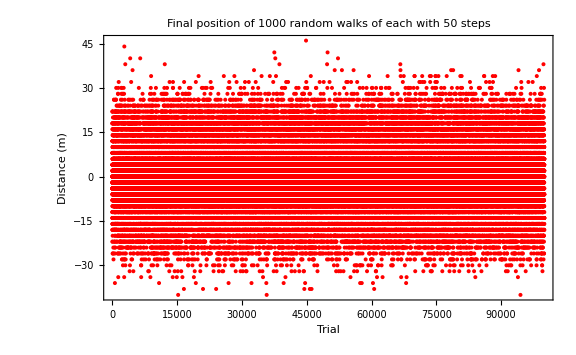

```mathematica
delx = 1; (*size of each step in m *)
nsteps = 50; (* number of steps *)
x = 0; (*initial position of particle *)
s= delx(2* RandomInteger[] -1); (* initial value of s *)
position=List[x];
i=0; 
k=0;
numberOf4s=0; 

(* 1000 random walks of 50 steps each *) 
While [k<1000000,
		m = 100; (* number of steps *) 
		i=0;
		While [ i <m,
		s = delx(2*RandomInteger[]-1);
		x = x+ s;
		i= i+1];
	     If [x==4, numberOf4s = numberOf4s +1,0];
	     position = Append[position,x]; (* x is the distance travelled in each 50 steps *) 
		x=0;
		k=k+1]
numberOf4s
probabilityOf4s = numberOf4s/1000000
position
i=0;
sum=0;
While[i<1000,
	  sum =sum +  (position[[i]])^2;
		i++]

meanSquared = (sum-List^2)/1000;
meanSquared
meanSD = 4 * 0.5 *0.5 * 50 * 1;
meanSD
		
		
ListPlot[position,PlotLabel -> (" Final position of 1000 random walks of each with 50 steps"),PlotRange->All,ImageSize->Large, Joined->False,Frame->True,FrameLabel->{"Trial","Distance (m)","",""},LabelStyle->(FontSize->14), PlotStyle->{RGBColor[1,0,0],PointSize[0.005]}]
```

{{62,62.},{26,26.},{87,87.},{70,70.},{100,100.},{91,91.},{96,96.},{65,65.},{38,38.},{37,37.},{5,5.},{3,3.},{71,71.},{78,78.},{48,48.},{20,20.},{0,0.},{29,29.},{19,19.},{29,29.},{76,76.},{90,90.},{27,27.},{83,83.},{90,90.},{18,18.},{21,21.},{66,66.},{67,67.},{47,47.},{23,23.},{45,45.},{67,67.},{55,55.},{12,12.},{70,70.},{15,15.},{19,19.},{97,97.},{2,2.},{7,7.},{83,83.},{52,52.},{36,36.},{90,90.},{9,9.},{4,4.},{3,3.},{83,83.},{79,79.},{77,77.},{99,99.},{44,44.},{61,61.},{12,12.},{2,2.},{2,2.},{41,41.},{48,48.},{42,42.},{38,38.},{52,52.},{56,56.},{30,30.},{13,13.},{83,83.},{92,92.},{77,77.},{61,61.},{28,28.},{65,65.},{90,90.},{59,59.},{46,46.},{72,72.},{15,15.},{15,15.},{15,15.},{45,45.},{100,100.},{63,63.},{13,13.},{39,39.},{86,86.},{3,3.},{89,89.},{78,78.},{31,31.},{29,29.},{25,25.},{4,4.},{13,13.},{35,35.},{68,68.},{3,3.},{63,63.},{50,50.},{55,55.},{22,22.},{46,46.},{45,45.},{48,48.},{99,99.},{88,88.},{13,13.},{30,30.},{32,32.},{36,36.},{3,3.},{72,72.},{43,43.},{2,2.},{9,9.},{21,21.},{27,27.},{23,23.},{48,48.},{68,68.},{69,69.},{89,89.},{77,77.},{80,80.},{63,63.},{90,90.},{63,63.},{53,53.},{24,24.},{65,65.},{56,56.},{83,83.},{97,97.},{79,79.},{15,15.},{77,77.},{26,26.},{51,51.},{45,45.},{60,60.},{94,94.},{22,22.},{35,35.},{52,52.},{37,37.},{72,72.},{31,31.},{17,17.},{91,91.},{73,73.},{0,0.},{76,76.},{11,11.},{78,78.},{98,98.},{62,62.},{56,56.},{77,77.},{49,49.},{37,37.},{75,75.},{78,78.},{63,63.},{56,56.},{77,77.},{59,59.},{81,81.},{59,59.},{52,52.},{65,65.},{42,42.},{0,0.},{84,84.},{78,78.},{32,32.},{54,54.},{40,40.},{26,26.},{54,54.},{32,32.},{74,74.},{49,49.},{31,31.},{84,84.},{35,35.},{43,43.},{7,7.},{57,57.},{49,49.},{7,7.},{62,62.},{1,1.},{88,88.},{51,51.},{94,94.},{90,90.},{35,35.},{24,24.},{20,20.},{36,36.},{56,56.},{30,30.},{78,78.},{14,14.},{32,32.},{22,22.},{61,61.},{23,23.},{36,36.},{6,6.},{73,73.},{50,50.},{81,81.},{13,13.},{38,38.},{29,29.},{74,74.},{88,88.},{44,44.},{62,62.},{93,93.},{49,49.},{40,40.},{64,64.},{27,27.},{16,16.},{97,97.},{22,22.},{26,26.},{88,88.},{83,83.},{84,84.},{13,13.},{42,42.},{30,30.},{5,5.},{73,73.},{64,64.},{52,52.},{1,1.},{63,63.},{46,46.},{28,28.},{12,12.},{74,74.},{25,25.},{46,46.},{97,97.},{9,9.},{79,79.},{7,7.},{53,53.},{55,55.},{38,38.},{6,6.},{29,29.},{74,74.},{100,100.},{45,45.},{27,27.},{34,34.},{61,61.},{41,41.},{73,73.},{21,21.},{25,25.},{89,89.},{33,33.},{5,5.},{31,31.},{60,60.},{81,81.},{64,64.},{58,58.},{32,32.},{25,25.},{0,0.},{18,18.},{73,73.},{79,79.},{50,50.},{96,96.},{86,86.},{23,23.},{75,75.},{100,100.},{54,54.},{1,1.},{32,32.},{92,92.},{16,16.},{25,25.},{64,64.},{30,30.},{15,15.},{5,5.},{9,9.},{78,78.},{68,68.},{95,95.},{14,14.},{55,55.},{33,33.},{15,15.},{90,90.},{38,38.},{16,16.},{27,27.},{56,56.},{59,59.},{93,93.},{17,17.},{4,4.},{4,4.},{52,52.},{95,95.},{68,68.},{51,51.},{58,58.},{4,4.},{8,8.},{10,10.},{83,83.},{91,91.},{27,27.},{33,33.},{39,39.},{41,41.},{9,9.},{99,99.},{63,63.},{74,74.},{49,49.},{31,31.},{81,81.},{44,44.},{7,7.},{3,3.},{16,16.},{81,81.},{50,50.},{34,34.},{35,35.},{76,76.},{55,55.},{6,6.},{91,91.},{87,87.},{61,61.},{100,100.},{29,29.},{1,1.},{6,6.},{3,3.},{21,21.},{56,56.},{61,61.},{69,69.},{67,67.},{55,55.},{40,40.},{62,62.},{72,72.},{65,65.},{24,24.},{86,86.},{82,82.},{64,64.},{81,81.},{24,24.},{27,27.},{62,62.},{77,77.},{44,44.},{9,9.},{57,57.},{15,15.},{13,13.},{80,80.},{52,52.},{7,7.},{38,38.},{22,22.},{37,37.},{75,75.},{100,100.},{6,6.},{79,79.},{6,6.},{1,1.},{95,95.},{3,3.},{68,68.},{78,78.},{4,4.},{58,58.},{47,47.},{48,48.},{26,26.},{26,26.},{34,34.},{59,59.},{91,91.},{3,3.},{74,74.},{94,94.},{96,96.},{27,27.},{39,39.},{22,22.},{66,66.},{75,75.},{50,50.},{95,95.},{65,65.},{11,11.},{34,34.},{34,34.},{52,52.},{80,80.},{36,36.},{98,98.},{69,69.},{37,37.},{31,31.},{19,19.},{12,12.},{48,48.},{31,31.},{6,6.},{62,62.},{35,35.},{76,76.},{82,82.},{38,38.},{27,27.},{21,21.},{85,85.},{69,69.},{52,52.},{15,15.},{79,79.},{3,3.},{61,61.},{56,56.},{2,2.},{72,72.},{55,55.},{23,23.},{9,9.},{54,54.},{44,44.},{12,12.},{51,51.},{70,70.},{51,51.},{11,11.},{3,3.},{5,5.},{85,85.},{42,42.},{74,74.},{38,38.},{22,22.},{14,14.},{52,52.},{27,27.},{95,95.},{1,1.},{74,74.},{53,53.},{10,10.},{26,26.},{24,24.},{7,7.},{68,68.},{60,60.},{52,52.},{74,74.},{17,17.},{90,90.},{77,77.},{65,65.},{67,67.},{78,78.},{19,19.},{62,62.},{56,56.},{67,67.},{19,19.},{61,61.},{51,51.},{32,32.},{58,58.},{80,80.},{64,64.},{26,26.},{25,25.},{59,59.},{97,97.},{85,85.},{74,74.},{97,97.},{67,67.},{12,12.},{88,88.},{28,28.},{81,81.},{65,65.},{49,49.},{96,96.},{27,27.},{52,52.},{31,31.},{90,90.},{100,100.},{10,10.},{16,16.},{66,66.},{41,41.},{75,75.},{21,21.},{50,50.},{83,83.},{71,71.},{67,67.},{10,10.},{27,27.},{44,44.},{9,9.},{55,55.},{48,48.},{28,28.},{22,22.},{92,92.},{8,8.},{95,95.},{63,63.},{45,45.},{67,67.},{65,65.},{81,81.},{85,85.},{3,3.},{60,60.},{9,9.},{96,96.},{24,24.},{38,38.},{10,10.},{58,58.},{78,78.},{20,20.},{6,6.},{89,89.},{94,94.},{67,67.},{40,40.},{82,82.},{71,71.},{31,31.},{35,35.},{35,35.},{16,16.},{92,92.},{79,79.},{99,99.},{11,11.},{64,64.},{9,9.},{58,58.},{33,33.},{83,83.},{78,78.},{62,62.},{14,14.},{33,33.},{0,0.},{9,9.},{3,3.},{14,14.},{35,35.},{77,77.},{20,20.},{13,13.},{17,17.},{61,61.},{46,46.},{53,53.},{49,49.},{87,87.},{13,13.},{53,53.},{20,20.},{99,99.},{35,35.},{96,96.},{84,84.},{87,87.},{1,1.},{45,45.},{51,51.},{79,79.},{25,25.},{22,22.},{22,22.},{26,26.},{30,30.},{25,25.},{63,63.},{0,0.},{100,100.},{81,81.},{2,2.},{66,66.},{21,21.},{36,36.},{79,79.},{11,11.},{82,82.},{81,81.},{48,48.},{42,42.},{76,76.},{92,92.},{87,87.},{99,99.},{73,73.},{40,40.},{67,67.},{85,85.},{93,93.},{2,2.},{29,29.},{23,23.},{64,64.},{27,27.},{66,66.},{37,37.},{10,10.},{74,74.},{86,86.},{47,47.},{65,65.},{7,7.},{18,18.},{22,22.},{38,38.},{65,65.},{99,99.},{69,69.},{83,83.},{37,37.},{63,63.},{3,3.},{66,66.},{28,28.},{96,96.},{11,11.},{75,75.},{75,75.},{92,92.},{65,65.},{87,87.},{84,84.},{61,61.},{36,36.},{50,50.},{73,73.},{35,35.},{24,24.},{83,83.},{66,66.},{31,31.},{95,95.},{87,87.},{38,38.},{55,55.},{57,57.},{78,78.},{26,26.},{48,48.},{95,95.},{50,50.},{68,68.},{67,67.},{3,3.},{37,37.},{61,61.},{31,31.},{1,1.},{8,8.},{13,13.},{70,70.},{34,34.},{96,96.},{90,90.},{10,10.},{20,20.},{61,61.},{70,70.},{53,53.},{53,53.},{81,81.},{42,42.},{16,16.},{20,20.},{8,8.},{43,43.},{6,6.},{13,13.},{88,88.},{46,46.},{7,7.},{0,0.},{36,36.},{83,83.},{79,79.},{10,10.},{47,47.},{1,1.},{90,90.},{63,63.},{16,16.},{52,52.},{41,41.},{44,44.},{60,60.},{16,16.},{15,15.},{17,17.},{38,38.},{92,92.},{39,39.},{34,34.},{26,26.},{86,86.},{68,68.},{34,34.},{95,95.},{55,55.},{11,11.},{64,64.},{29,29.},{34,34.},{40,40.},{61,61.},{96,96.},{27,27.},{33,33.},{19,19.},{28,28.},{41,41.},{52,52.},{86,86.},{20,20.},{88,88.},{84,84.},{72,72.},{6,6.},{19,19.},{91,91.},{2,2.},{18,18.},{96,96.},{90,90.},{56,56.},{53,53.},{6,6.},{2,2.},{34,34.},{85,85.},{98,98.},{15,15.},{99,99.},{37,37.},{38,38.},{36,36.},{28,28.},{4,4.},{94,94.},{41,41.},{11,11.},{46,46.},{46,46.},{28,28.},{84,84.},{44,44.},{12,12.},{51,51.},{66,66.},{12,12.},{22,22.},{29,29.},{60,60.},{78,78.},{40,40.},{84,84.},{96,96.},{2,2.},{70,70.},{58,58.},{40,40.},{49,49.},{17,17.},{44,44.},{34,34.},{20,20.},{4,4.},{6,6.},{26,26.},{92,92.},{91,91.},{33,33.},{60,60.},{14,14.},{26,26.},{78,78.},{46,46.},{60,60.},{52,52.},{28,28.},{62,62.},{67,67.},{40,40.},{92,92.},{31,31.},{13,13.},{10,10.},{96,96.},{17,17.},{39,39.},{39,39.},{59,59.},{31,31.},{67,67.},{40,40.},{66,66.},{87,87.},{5,5.},{97,97.},{10,10.},{95,95.},{53,53.},{61,61.},{50,50.},{52,52.},{41,41.},{53,53.},{47,47.},{79,79.},{58,58.},{96,96.},{30,30.},{51,51.},{46,46.},{39,39.},{35,35.},{87,87.},{89,89.},{25,25.},{94,94.},{7,7.},{29,29.},{63,63.},{37,37.},{55,55.},{73,73.},{32,32.},{9,9.},{70,70.},{0,0.},{73,73.},{82,82.},{72,72.},{80,80.},{97,97.},{36,36.},{60,60.},{54,54.},{68,68.},{26,26.},{15,15.},{58,58.},{36,36.},{33,33.},{14,14.},{94,94.},{69,69.},{12,12.},{100,100.},{91,91.},{30,30.},{53,53.},{99,99.},{68,68.},{66,66.},{70,70.},{80,80.},{81,81.},{93,93.},{1,1.},{75,75.},{8,8.},{23,23.},{46,46.},{61,61.},{48,48.},{81,81.},{7,7.},{54,54.},{56,56.},{61,61.},{5,5.},{33,33.},{11,11.},{60,60.},{29,29.},{35,35.},{52,52.},{31,31.},{96,96.},{0,0.},{52,52.},{38,38.},{5,5.},{10,10.},{77,77.},{55,55.},{74,74.},{53,53.},{75,75.},{97,97.},{11,11.},{53,53.},{51,51.},{59,59.},{86,86.},{75,75.},{95,95.},{26,26.},{71,71.},{55,55.},{23,23.},{11,11.},{74,74.},{46,46.},{36,36.},{43,43.},{30,30.},{19,19.},{25,25.},{50,50.},{60,60.},{88,88.},{81,81.},{90,90.},{95,95.},{12,12.},{28,28.},{51,51.},{80,80.},{34,34.},{94,94.},{64,64.},{52,52.},{11,11.},{1,1.},{73,73.},{97,97.},{59,59.},{93,93.},{37,37.},{2,2.},{94,94.},{27,27.},{88,88.},{66,66.},{10,10.},{65,65.},{90,90.},{60,60.},{71,71.},{95,95.},{37,37.},{14,14.},{27,27.},{91,91.},{85,85.},{69,69.},{42,42.},{70,70.},{32,32.},{94,94.},{52,52.},{12,12.},{18,18.},{10,10.},{11,11.},{71,71.},{85,85.},{66,66.}}

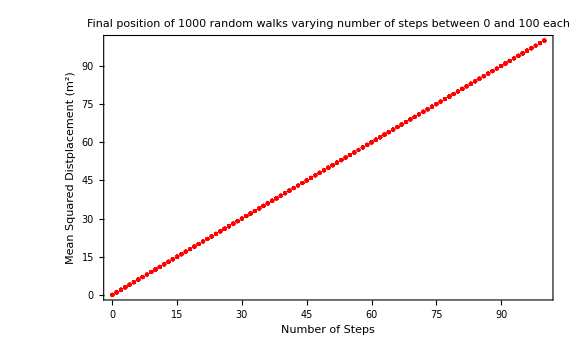

```mathematica
(* 1000 random walks of varying number of steps between 0 and 50 each*) 
meanSquared = List[];
l=0; 
While [ l <1000,
	meanSD = 0;
	sum = 0; 
	m = RandomInteger[{0,100}]; (* number of steps *) 
	k=0;
	While [k<1000,
			i=0;
			x=0;
				While [ i <m,
				s = delx(2*RandomInteger[]-1);
				x = x+ s; 
				i= i+1];
	                    sum =sum + x;
			k=k+1];
		(*meanSD = ((sum)/1000)^2;*)
		meanSD = 4 * 0.5 *0.5 * m *delx^2;
		meanSquared = Append[meanSquared,{m,meanSD}];
	     l++]; (* x is the distance travelled in each 50 steps *) 
		
meanSquared

(*
i=0;
sum=0;
While[i<1000,
	  sum =sum +  position[[i]];
		i++]

average = (sum-List)/1000;
meanSquared = ((sum-List)/1000)^2;
meanSquared*)
		
		
ListPlot[meanSquared, PlotRange-> All, PlotLabel -> (" Final position of 1000 random walks varying number of steps between 0 and 100 each"),PlotRange->All,ImageSize->Large, Joined->False,Frame->True,FrameLabel->{"Number of Steps","Mean Squared Distplacement (m^2)","",""},LabelStyle->(FontSize->14), PlotStyle->{RGBColor[1,0,0],PointSize[0.005]}]
```

```mathematica
(* The final position is irrespective of the number of steps as long as the simulation is run for a significantly long time, so we are dealing with big distributions *)
```

```mathematica
(* 1000 random walks of varying number of steps between 0 and 50 each*) 
meanSquaredVsStepSize = List[];
l=0; 
While [ l <1000,
	meanSD = 0;
	sum = 0; 
	m = 50; (* number of steps *) 
	k=0;
	delx = RandomInteger[{0,100}];
	While [k<100,
			i=0;
			x=0;
				While [ i <m,
				s = delx(2*RandomInteger[]-1);
				x = x+ s; 
				i= i+1];
	                    sum =sum + x;
			k=k+1];
		(*meanSD = ((sum)/100)^2;*)
		meanSD = 4 *0.5*0.5*50*delx^2;
		meanSquaredVsStepSize = Append[meanSquaredVsStepSize,{delx,meanSD}];
	     l++]; (* x is the distance travelled in each 50 steps *) 
		
meanSquaredVsStepSize
```

{{99,490050.},{45,101250.},{86,369800.},{87,378450.},{53,140450.},{20,20000.},{17,14450.},{48,115200.},{66,217800.},{37,68450.},{95,451250.},{10,5000.},{9,4050.},{82,336200.},{97,470450.},{58,168200.},{99,490050.},{70,245000.},{54,145800.},{26,33800.},{83,344450.},{22,24200.},{3,450.},{26,33800.},{90,405000.},{90,405000.},{74,273800.},{88,387200.},{62,192200.},{71,252050.},{66,217800.},{25,31250.},{18,16200.},{89,396050.},{43,92450.},{61,186050.},{41,84050.},{27,36450.},{49,120050.},{62,192200.},{29,42050.},{99,490050.},{50,125000.},{70,245000.},{71,252050.},{100,500000.},{53,140450.},{12,7200.},{93,432450.},{63,198450.},{61,186050.},{78,304200.},{99,490050.},{33,54450.},{78,304200.},{33,54450.},{10,5000.},{89,396050.},{31,48050.},{5,1250.},{26,33800.},{68,231200.},{70,245000.},{83,344450.},{74,273800.},{0,0.},{64,204800.},{49,120050.},{38,72200.},{46,105800.},{5,1250.},{100,500000.},{55,151250.},{95,451250.},{42,88200.},{30,45000.},{97,470450.},{6,1800.},{97,470450.},{70,245000.},{31,48050.},{100,500000.},{44,96800.},{86,369800.},{19,18050.},{40,80000.},{57,162450.},{41,84050.},{39,76050.},{61,186050.},{37,68450.},{5,1250.},{48,115200.},{38,72200.},{63,198450.},{43,92450.},{21,22050.},{62,192200.},{41,84050.},{9,4050.},{20,20000.},{0,0.},{79,312050.},{7,2450.},{62,192200.},{3,450.},{70,245000.},{54,145800.},{62,192200.},{30,45000.},{80,320000.},{59,174050.},{30,45000.},{32,51200.},{67,224450.},{57,162450.},{81,328050.},{89,396050.},{21,22050.},{65,211250.},{56,156800.},{94,441800.},{9,4050.},{77,296450.},{16,12800.},{46,105800.},{27,36450.},{23,26450.},{73,266450.},{13,8450.},{96,460800.},{0,0.},{40,80000.},{92,423200.},{64,204800.},{39,76050.},{82,336200.},{51,130050.},{26,33800.},{46,105800.},{89,396050.},{48,115200.},{35,61250.},{78,304200.},{96,460800.},{59,174050.},{9,4050.},{81,328050.},{15,11250.},{63,198450.},{63,198450.},{15,11250.},{18,16200.},{20,20000.},{35,61250.},{28,39200.},{4,800.},{77,296450.},{26,33800.},{75,281250.},{17,14450.},{14,9800.},{52,135200.},{69,238050.},{16,12800.},{65,211250.},{17,14450.},{75,281250.},{69,238050.},{61,186050.},{51,130050.},{82,336200.},{60,180000.},{97,470450.},{80,320000.},{25,31250.},{97,470450.},{34,57800.},{61,186050.},{93,432450.},{97,470450.},{84,352800.},{64,204800.},{74,273800.},{22,24200.},{19,18050.},{90,405000.},{40,80000.},{5,1250.},{34,57800.},{24,28800.},{22,24200.},{81,328050.},{95,451250.},{6,1800.},{36,64800.},{99,490050.},{39,76050.},{97,470450.},{62,192200.},{17,14450.},{29,42050.},{94,441800.},{17,14450.},{13,8450.},{10,5000.},{32,51200.},{53,140450.},{78,304200.},{75,281250.},{92,423200.},{49,120050.},{49,120050.},{88,387200.},{32,51200.},{70,245000.},{52,135200.},{85,361250.},{98,480200.},{60,180000.},{35,61250.},{82,336200.},{97,470450.},{9,4050.},{54,145800.},{46,105800.},{29,42050.},{5,1250.},{67,224450.},{24,28800.},{76,288800.},{66,217800.},{100,500000.},{80,320000.},{100,500000.},{18,16200.},{59,174050.},{14,9800.},{39,76050.},{100,500000.},{69,238050.},{95,451250.},{79,312050.},{69,238050.},{58,168200.},{24,28800.},{52,135200.},{76,288800.},{36,64800.},{27,36450.},{47,110450.},{56,156800.},{40,80000.},{62,192200.},{79,312050.},{51,130050.},{2,200.},{98,480200.},{0,0.},{66,217800.},{25,31250.},{37,68450.},{93,432450.},{24,28800.},{33,54450.},{5,1250.},{61,186050.},{83,344450.},{32,51200.},{60,180000.},{10,5000.},{70,245000.},{90,405000.},{67,224450.},{48,115200.},{87,378450.},{70,245000.},{52,135200.},{34,57800.},{95,451250.},{71,252050.},{14,9800.},{90,405000.},{72,259200.},{76,288800.},{36,64800.},{94,441800.},{61,186050.},{18,16200.},{28,39200.},{86,369800.},{36,64800.},{41,84050.},{29,42050.},{11,6050.},{31,48050.},{63,198450.},{100,500000.},{73,266450.},{25,31250.},{22,24200.},{8,3200.},{55,151250.},{66,217800.},{52,135200.},{96,460800.},{14,9800.},{71,252050.},{6,1800.},{59,174050.},{91,414050.},{47,110450.},{49,120050.},{33,54450.},{78,304200.},{76,288800.},{79,312050.},{18,16200.},{84,352800.},{89,396050.},{30,45000.},{60,180000.},{39,76050.},{31,48050.},{62,192200.},{22,24200.},{52,135200.},{56,156800.},{17,14450.},{78,304200.},{9,4050.},{87,378450.},{4,800.},{4,800.},{28,39200.},{2,200.},{85,361250.},{43,92450.},{16,12800.},{24,28800.},{86,369800.},{52,135200.},{91,414050.},{76,288800.},{45,101250.},{96,460800.},{62,192200.},{63,198450.},{88,387200.},{52,135200.},{66,217800.},{40,80000.},{85,361250.},{28,39200.},{89,396050.},{11,6050.},{21,22050.},{66,217800.},{22,24200.},{100,500000.},{79,312050.},{91,414050.},{21,22050.},{37,68450.},{56,156800.},{97,470450.},{57,162450.},{2,200.},{3,450.},{10,5000.},{84,352800.},{12,7200.},{48,115200.},{5,1250.},{95,451250.},{10,5000.},{33,54450.},{88,387200.},{26,33800.},{5,1250.},{32,51200.},{85,361250.},{53,140450.},{84,352800.},{62,192200.},{57,162450.},{76,288800.},{75,281250.},{5,1250.},{30,45000.},{83,344450.},{98,480200.},{27,36450.},{27,36450.},{30,45000.},{18,16200.},{44,96800.},{36,64800.},{15,11250.},{20,20000.},{6,1800.},{18,16200.},{15,11250.},{30,45000.},{10,5000.},{74,273800.},{94,441800.},{24,28800.},{65,211250.},{96,460800.},{93,432450.},{89,396050.},{93,432450.},{99,490050.},{26,33800.},{51,130050.},{7,2450.},{75,281250.},{10,5000.},{60,180000.},{53,140450.},{44,96800.},{15,11250.},{33,54450.},{91,414050.},{41,84050.},{49,120050.},{20,20000.},{22,24200.},{91,414050.},{5,1250.},{74,273800.},{49,120050.},{56,156800.},{21,22050.},{62,192200.},{25,31250.},{26,33800.},{49,120050.},{28,39200.},{28,39200.},{0,0.},{19,18050.},{9,4050.},{92,423200.},{36,64800.},{62,192200.},{18,16200.},{15,11250.},{49,120050.},{99,490050.},{60,180000.},{54,145800.},{36,64800.},{1,50.},{59,174050.},{23,26450.},{52,135200.},{13,8450.},{56,156800.},{77,296450.},{15,11250.},{49,120050.},{58,168200.},{98,480200.},{76,288800.},{18,16200.},{46,105800.},{32,51200.},{72,259200.},{23,26450.},{32,51200.},{45,101250.},{35,61250.},{37,68450.},{59,174050.},{39,76050.},{96,460800.},{40,80000.},{9,4050.},{19,18050.},{86,369800.},{88,387200.},{42,88200.},{18,16200.},{59,174050.},{95,451250.},{95,451250.},{86,369800.},{55,151250.},{1,50.},{66,217800.},{61,186050.},{17,14450.},{12,7200.},{53,140450.},{82,336200.},{35,61250.},{97,470450.},{7,2450.},{38,72200.},{37,68450.},{73,266450.},{30,45000.},{70,245000.},{89,396050.},{75,281250.},{95,451250.},{7,2450.},{56,156800.},{7,2450.},{33,54450.},{44,96800.},{48,115200.},{95,451250.},{60,180000.},{44,96800.},{39,76050.},{50,125000.},{92,423200.},{42,88200.},{59,174050.},{21,22050.},{94,441800.},{31,48050.},{6,1800.},{69,238050.},{92,423200.},{59,174050.},{89,396050.},{34,57800.},{73,266450.},{39,76050.},{72,259200.},{79,312050.},{78,304200.},{3,450.},{81,328050.},{73,266450.},{30,45000.},{39,76050.},{58,168200.},{25,31250.},{70,245000.},{10,5000.},{24,28800.},{6,1800.},{74,273800.},{24,28800.},{81,328050.},{11,6050.},{25,31250.},{39,76050.},{7,2450.},{16,12800.},{96,460800.},{13,8450.},{50,125000.},{40,80000.},{97,470450.},{67,224450.},{75,281250.},{63,198450.},{70,245000.},{38,72200.},{35,61250.},{27,36450.},{84,352800.},{40,80000.},{58,168200.},{11,6050.},{40,80000.},{34,57800.},{85,361250.},{29,42050.},{86,369800.},{94,441800.},{28,39200.},{1,50.},{75,281250.},{62,192200.},{42,88200.},{92,423200.},{15,11250.},{95,451250.},{23,26450.},{64,204800.},{32,51200.},{19,18050.},{41,84050.},{67,224450.},{57,162450.},{24,28800.},{41,84050.},{47,110450.},{35,61250.},{37,68450.},{98,480200.},{27,36450.},{91,414050.},{52,135200.},{1,50.},{75,281250.},{39,76050.},{18,16200.},{93,432450.},{64,204800.},{92,423200.},{37,68450.},{44,96800.},{51,130050.},{25,31250.},{77,296450.},{60,180000.},{21,22050.},{87,378450.},{54,145800.},{37,68450.},{13,8450.},{53,140450.},{64,204800.},{31,48050.},{2,200.},{33,54450.},{4,800.},{18,16200.},{6,1800.},{22,24200.},{11,6050.},{63,198450.},{91,414050.},{53,140450.},{25,31250.},{41,84050.},{20,20000.},{65,211250.},{76,288800.},{7,2450.},{11,6050.},{47,110450.},{97,470450.},{74,273800.},{6,1800.},{15,11250.},{98,480200.},{81,328050.},{64,204800.},{95,451250.},{96,460800.},{76,288800.},{8,3200.},{81,328050.},{74,273800.},{32,51200.},{94,441800.},{60,180000.},{77,296450.},{68,231200.},{29,42050.},{79,312050.},{84,352800.},{63,198450.},{84,352800.},{52,135200.},{89,396050.},{92,423200.},{25,31250.},{22,24200.},{21,22050.},{72,259200.},{67,224450.},{27,36450.},{27,36450.},{5,1250.},{35,61250.},{62,192200.},{93,432450.},{27,36450.},{68,231200.},{10,5000.},{74,273800.},{62,192200.},{67,224450.},{51,130050.},{24,28800.},{47,110450.},{17,14450.},{89,396050.},{47,110450.},{2,200.},{14,9800.},{50,125000.},{28,39200.},{18,16200.},{69,238050.},{83,344450.},{37,68450.},{30,45000.},{26,33800.},{28,39200.},{99,490050.},{41,84050.},{56,156800.},{53,140450.},{0,0.},{60,180000.},{26,33800.},{58,168200.},{66,217800.},{39,76050.},{19,18050.},{51,130050.},{44,96800.},{44,96800.},{94,441800.},{57,162450.},{44,96800.},{6,1800.},{45,101250.},{94,441800.},{76,288800.},{29,42050.},{57,162450.},{35,61250.},{52,135200.},{64,204800.},{70,245000.},{26,33800.},{87,378450.},{38,72200.},{9,4050.},{27,36450.},{71,252050.},{27,36450.},{66,217800.},{30,45000.},{36,64800.},{3,450.},{68,231200.},{4,800.},{87,378450.},{98,480200.},{47,110450.},{33,54450.},{36,64800.},{15,11250.},{89,396050.},{55,151250.},{100,500000.},{46,105800.},{9,4050.},{18,16200.},{20,20000.},{9,4050.},{23,26450.},{35,61250.},{35,61250.},{35,61250.},{34,57800.},{77,296450.},{9,4050.},{76,288800.},{38,72200.},{82,336200.},{66,217800.},{35,61250.},{30,45000.},{71,252050.},{97,470450.},{25,31250.},{31,48050.},{47,110450.},{54,145800.},{42,88200.},{87,378450.},{97,470450.},{70,245000.},{31,48050.},{76,288800.},{41,84050.},{25,31250.},{8,3200.},{4,800.},{60,180000.},{29,42050.},{6,1800.},{27,36450.},{71,252050.},{74,273800.},{40,80000.},{50,125000.},{67,224450.},{21,22050.},{9,4050.},{23,26450.},{97,470450.},{26,33800.},{1,50.},{50,125000.},{66,217800.},{3,450.},{84,352800.},{0,0.},{86,369800.},{80,320000.},{60,180000.},{33,54450.},{6,1800.},{49,120050.},{29,42050.},{88,387200.},{36,64800.},{13,8450.},{77,296450.},{25,31250.},{73,266450.},{52,135200.},{6,1800.},{50,125000.},{63,198450.},{67,224450.},{90,405000.},{65,211250.},{43,92450.},{40,80000.},{85,361250.},{36,64800.},{21,22050.},{43,92450.},{62,192200.},{73,266450.},{89,396050.},{67,224450.},{5,1250.},{28,39200.},{29,42050.},{20,20000.},{4,800.},{42,88200.},{85,361250.},{99,490050.},{23,26450.},{47,110450.},{3,450.},{26,33800.},{53,140450.},{28,39200.},{100,500000.},{21,22050.},{58,168200.},{57,162450.},{32,51200.},{89,396050.},{40,80000.},{34,57800.},{18,16200.},{29,42050.},{79,312050.},{2,200.},{14,9800.},{59,174050.},{86,369800.},{36,64800.},{5,1250.},{41,84050.},{100,500000.},{68,231200.},{93,432450.},{31,48050.},{28,39200.},{61,186050.},{40,80000.},{22,24200.},{20,20000.},{53,140450.},{65,211250.},{60,180000.},{33,54450.},{63,198450.},{5,1250.},{17,14450.},{37,68450.},{47,110450.},{87,378450.},{79,312050.},{64,204800.},{15,11250.},{46,105800.},{31,48050.},{0,0.},{11,6050.},{54,145800.},{91,414050.},{6,1800.},{6,1800.},{2,200.},{49,120050.},{82,336200.},{53,140450.},{64,204800.},{79,312050.},{14,9800.},{1,50.},{20,20000.},{57,162450.},{37,68450.},{30,45000.},{55,151250.},{61,186050.},{82,336200.},{0,0.},{26,33800.},{66,217800.},{73,266450.},{62,192200.},{90,405000.},{31,48050.},{6,1800.},{4,800.},{87,378450.},{79,312050.},{32,51200.},{46,105800.},{16,12800.},{50,125000.},{71,252050.},{17,14450.},{14,9800.},{50,125000.},{65,211250.},{8,3200.},{72,259200.},{23,26450.},{97,470450.},{44,96800.},{1,50.},{100,500000.},{89,396050.},{86,369800.},{38,72200.},{97,470450.},{37,68450.},{58,168200.},{74,273800.},{90,405000.},{42,88200.},{30,45000.},{28,39200.},{37,68450.},{55,151250.},{13,8450.},{21,22050.},{32,51200.},{43,92450.},{31,48050.},{86,369800.},{99,490050.},{19,18050.},{45,101250.},{19,18050.},{58,168200.},{7,2450.},{36,64800.},{69,238050.},{8,3200.},{9,4050.},{2,200.},{16,12800.},{12,7200.},{97,470450.},{48,115200.},{34,57800.},{20,20000.},{49,120050.},{41,84050.},{12,7200.},{28,39200.},{67,224450.},{35,61250.},{12,7200.},{85,361250.},{5,1250.},{52,135200.},{68,231200.},{63,198450.},{49,120050.},{47,110450.},{79,312050.},{13,8450.},{32,51200.},{10,5000.},{9,4050.},{52,135200.},{51,130050.},{61,186050.},{15,11250.},{29,42050.},{64,204800.},{38,72200.},{81,328050.}}

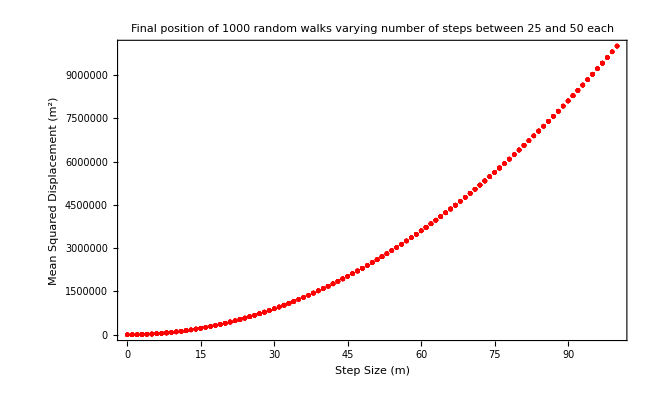

```mathematica
ListPlot[meanSquaredVsStepSize, PlotRange->All, PlotLabel -> (" Final position of 1000 random walks varying number of steps between 25 and 50 each"),PlotRange->All,ImageSize->Large, Joined->False,Frame->True,FrameLabel->{"Step Size (m)","Mean Squared Displacement (m^2)","",""},LabelStyle->(FontSize->14), PlotStyle->{RGBColor[1,0,0],PointSize[0.005]}]
```

```mathematica
(* As the step size increases the mean squared distance travelled increases as well *)
```